This file is copied from the github directory accompanying the paper arXiv:1810.06160v2
https://github.com/mbabiuc/MathScripts

# Inspiral Phase Time Evolution

## Variables and Constants

```mathematica
Off[General::spell];
```

```mathematica
SetOptions[Simplify,TimeConstraint->1000];
```

```mathematica
ClearAll["Global`*"]
```

#### Setting up the Mass Parameters

Change here the mass parameters

```mathematica
m1=20; m2=20;
```

```mathematica
q=m1/m2; M=m1+m2; μ=(m1*m2)/M;η=μ/M;
```

Geometric Units

```mathematica
Ms = M*(4.923*10^(-6));(*Expressing mass in seconds*)
```

```mathematica
Mr = M*(1.476);(*Expressing mass in kilometers*)
```

```mathematica
G=c=1 ;(*we work in geometric units*)
```

```mathematica
γ=0.5772156649;
```

```mathematica
e = 0;(*eccentricity*)
```

```mathematica
R = 1; (*Distance to the observer - Can change R to fit as desired*)
```

```mathematica
i = 0;κ=0; (*assume optimal orientation of observer*)
```

```mathematica
flow=10; (* cut-off frequency of 10 Hz *)
```

```mathematica
G=6.673 10^-11; c=2.998 10^8;
Subscript[M, okg]=1.989 10^30; Subscript[M, os]=4.923 10^-6; Subscript[M, okm]=1.476; (*Expressing mass in kg, sec. or km*)
```

```mathematica
Ms=M*Subscript[M, os]; Mr=M*Subscript[M, okm];(*mass in seconds and kilometers*)
```

```mathematica
v0=N[(G*M*Subscript[M, okg]*Pi*flow)^(1/3)](*initial binary velocity*)
```

5.50455×10^7

Integration Bounds

```mathematica
temp=100 (*temporary finalintegration time, set up to something bigtime *)
```

100

```mathematica
xlow=N[(Pi*M*Subscript[M, os]*flow)^(2/3)]
```

0.0336997

```mathematica
xhigh =N[ 1/6(1+7/18 η)](* 2nd order PN xhigh *)
```

0.18287

First Level, constants

```mathematica
α0=153.8803; α1=-55.13; α2=588; α3=-1144;
```

### Second level, depending on the symmetric mass ratio

```mathematica
a4=-5η*α0-(97 η^4)/3888-(18929389 η^3)/435456-(3157 π^2*η^2)/144+(54732199 η^2)/93312-47468/315*η*Log[x[t]]-(31495 π^2*η)/8064-(856γ*η)/315+(59292668653η)/838252800-1712/315 η*Log[2]+(124741Log[x[t]])/8820-(361 π^2)/126+(124741γ)/4410+3959271176713/25427001600-(47385Log[3])/1568+(127751Log[2])/1470
```

7.61819-(41507 Log[x[t]])/1764

```mathematica
a4p5=(9731π*η^3)/1344+(42680611π*η^2)/145152+(205 π^3 η)/6-(51438847π*η)/48384-3424/105 π*Log[x[t]]-(6848γ*π)/105+(343801320119π)/745113600-13696/105 π*Log[2]
```

535.198-3424/105 π Log[x[t]]

```mathematica
a5=(155α0*η^2)/12+(1195α0*η)/336-6η*α1-(11567 η^5)/62208+(51474823 η^4)/1741824+(9799 π^2*η^3)/384-(9007776763 η^3)/11757312+216619/189 η^2*Log[x[t]]-(126809 π^2*η^2)/3024-(2354γ*η^2)/945+(1362630004933 η^2)/914457600-4708/945 η^2*Log[2]+(53963197η*Log[x[t]])/52920+(14555455 π^2*η)/217728+(3090781γ*η)/26460-(847101477593593η)/228843014400-(15795η*Log[3])/3136+(2105111η*Log[2])/8820-(5910592*Log[x[t]])/1964655-(21512 π^2)/1701-(11821184γ)/1964655+29619150939541789/36248733480960+(616005Log[3])/3136-(107638990Log[2])/392931
```

413.882+(4068287915 Log[x[t]])/12573792

```mathematica
a5p5=-20*π*η*α0+(49187π*η^4)/6048-(7030123π*η^3)/13608-(112955 π^3*η^2)/576+(1760705531π*η^2)/290304-189872/315 π*η*Log[x[t]]-(26035 π^3*η)/16128-(3424γ*π*η)/315-(2437749208561π*η)/4470681600-6848/315 π*η*Log[2]+(311233π*Log[x[t]])/11760+(311233γ*π)/5880+(91347297344213π)/81366405120-142155/784 π*Log[3]+(5069891π*Log[2])/17640
```

1533.9-(4382717 π Log[x[t]])/35280

```mathematica
a6=-(535α0*η^3)/36+(7295α0*η^2)/336-(248065α0*η)/4536+(31α1*η^2)/2+(239α1*η)/56-7α2*η-7α3*η*Log[x[t]]-α3*η-(155377 η^6)/1679616-(152154269 η^5)/10450944-(1039145 π^2*η^4)/62208+(76527233921 η^4)/94058496-(41026693 η^3*Log[x[t]])/17010+(55082725 π^2*η^3)/217728-(2033γ*η^3)/1701-(56909847373567 η^3)/7242504192-(4066 η^3*Log[2])/1701-(271237829 η^2*Log[x[t]])/127008+(92455 π^4*η^2)/1152-(4061971769 π^2*η^2)/870912-(21169753γ*η^2)/317520+(3840832667727673 η^2)/55477094400-(57915 η^2*Log[3])/12544-(2724535 η^2*Log[2])/21168-4387/63 π^2*η*Log[x[t]]-(12030840839η*Log[x[t]])/37721376+(410 π^4*η)/9-8774/63 γ*π^2*η+(206470485307 π^2*η)/1005903360+(362623282541γ*η)/94303440-(12413297162366594971η)/271865501107200+(3016845η*Log[3])/12544-17548/63 π^2*η*Log[2]+(701463800861η*Log[2])/94303440+(366368 Log[x[t]]^2)/11025+(2930944Log[2]Log[x[t]])/11025-13696/315 π^2*Log[x[t]]+(1465472γ*Log[x[t]])/11025-(155359670313691Log[x[t]])/157329572400-(27392*N[Zeta[3],25])/105-(256 π^4)/45-(27392γ*π^2)/315+(1414520047 π^2)/2619540+(1465472 γ^2)/11025-(155359670313691γ)/78664786200+1867705968412371074441833/154211174411374080000+(5861888 Log[2]^2)/11025-(37744140625Log[5])/260941824-(63722699919Log[3])/112752640-54784/315 π^2*Log[2]+(5861888γ*Log[2])/11025-(206962178724547Log[2])/78664786200
```

2082.23+423.679 Log[x[t]]+(366368 Log[x[t]]^2)/11025

Calculating PN Parameter-x for e =0 (zero eccentricity)

```mathematica
Expr3p5PN[t_]=64/5 η*x[t]^5*(1+(-743/336-11/4 η)*x[t]+4π*x[t]^(3/2)+(34103/18144+13661/2016 η+59/18 η^2)*x[t]^2
+((-4159π)/672-(189π)/8*η)*x[t]^(5/2)
+(16447322263/139708800-(1712γ)/105+(16 π^2)/3
-856/105*Log[16*x[t]]+(-56198689/217728+(451 π^2)/48)η
+541/896 η^2-5605/2592 η^3)x[t]^3)+(64π)/5*η*x[t]^5*(-4415/4032+358675/6048 η+91945/1512 η^2)x[t]^(7/2)
```

6059/108 π x[t]^(17/2)+16/5 x[t]^5 (1-(487 x[t])/168+4 π x[t]^(3/2)+(274229 x[t]^2)/72576-254/21 π x[t]^(5/2)+(119.611-856/105 Log[16 x[t]]) x[t]^3)

```mathematica
Expr4to6[t_]=(64η*x[t]^5)/5(a4*x[t]^4+a4p5*x[t]^(9/2)+a5*x[t]^5+a5p5*x[t]^(11/2)+a6*x[t]^6)
```

16/5 x[t]^5 ((7.61819-(41507 Log[x[t]])/1764) x[t]^4+(535.198-3424/105 π Log[x[t]]) x[t]^(9/2)+(413.882+(4068287915 Log[x[t]])/12573792) x[t]^5+(1533.9-(4382717 π Log[x[t]])/35280) x[t]^(11/2)+(2082.23+423.679 Log[x[t]]+(366368 Log[x[t]]^2)/11025) x[t]^6)

```mathematica
(*dx/dt*)
```

```mathematica
Expr6PN=Expand[Simplify[(Expr3p5PN[t]+Expr4to6[t])/Ms]]
```

16250.3 x[t]^5-47106.4 x[t]^6+204207. x[t]^(13/2)+61401.7 x[t]^7-617482. x[t]^(15/2)+1.5764×10^6 x[t]^8-132478. Log[x[t]] x[t]^8+895029. x[t]^(17/2)+123797. x[t]^9-382369. Log[x[t]] x[t]^9+8.6971×10^6 x[t]^(19/2)-1.66477×10^6 Log[x[t]] x[t]^(19/2)+6.72569×10^6 x[t]^10+5.25782×10^6 Log[x[t]] x[t]^10+2.49262×10^7 x[t]^(21/2)-6.34198×10^6 Log[x[t]] x[t]^(21/2)+3.38368×10^7 x[t]^11+6.88488×10^6 Log[x[t]] x[t]^11+540007. Log[x[t]]^2 x[t]^11

```mathematica
(*Numerically solving a differential equation to find PN parameter x*)
```

#### Setting up the final integration time

```mathematica
Expr6PN
```

16250.3 x[t]^5-47106.4 x[t]^6+204207. x[t]^(13/2)+61401.7 x[t]^7-617482. x[t]^(15/2)+1.5764×10^6 x[t]^8-132478. Log[x[t]] x[t]^8+895029. x[t]^(17/2)+123797. x[t]^9-382369. Log[x[t]] x[t]^9+8.6971×10^6 x[t]^(19/2)-1.66477×10^6 Log[x[t]] x[t]^(19/2)+6.72569×10^6 x[t]^10+5.25782×10^6 Log[x[t]] x[t]^10+2.49262×10^7 x[t]^(21/2)-6.34198×10^6 Log[x[t]] x[t]^(21/2)+3.38368×10^7 x[t]^11+6.88488×10^6 Log[x[t]] x[t]^11+540007. Log[x[t]]^2 x[t]^11

```mathematica
solx =NDSolve[{x'[t]-Expr6PN
==0,x[0]==xlow},x,{t,0,temp}]
```

NDSolve::ndsz: At t == 11.9248, step size is effectively zero; singularity or stiff system suspected.

{{x→InterpolatingFunction[…]}}

Change the stiff time here

```mathematica
tS=11.924777117026338 (*copy the stiff time here*)
```

11.9248

```mathematica
tF=2*Ms; Tfin=tS-tF
```

11.9244

```mathematica
solx =NDSolve[{x'[t]-Expr6PN
==0,x[0]==xlow},x,{t,0,Tfin}]
```

{{x→InterpolatingFunction[…]}}

```mathematica
xins[t_]=Evaluate[x[t]/.solx]
```

{InterpolatingFunction[…][t]}

```mathematica
xins[Tfin]
```

{0.245018}

```mathematica
Tinit=Tfin-1.
```

10.9244

## Final Time is chosen where the Strain hits its last peak before the DE becomes too “stiff”

```mathematica
xins[t_]=Evaluate[x[t]/.solx]
```

{InterpolatingFunction[…][t]}

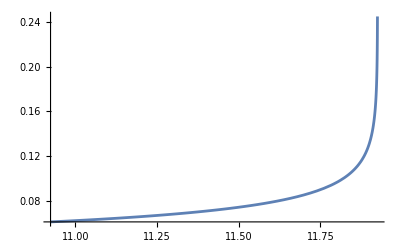

```mathematica
Plot[xins[t],{t,Tinit, Tfin},PlotRange->All]
```

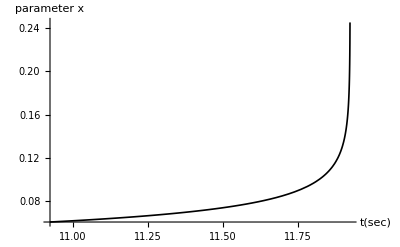

```mathematica
Plot[xins [t],{t,Tinit,Tfin},PlotStyle->{Thickness[0.003],Black}, PlotRange->All,AxesLabel->{t[sec],parameter x }]
```

### Orbital Frequency Evolution

```mathematica
omega[t_]:=xins[t]^(3/2)/Ms
```

```mathematica
fGW[t_]:= omega[t]/π
```

```mathematica
fpGW[t_]:=fGW'[t]
```

```mathematica
omega[Tfin]
```

{615.895}

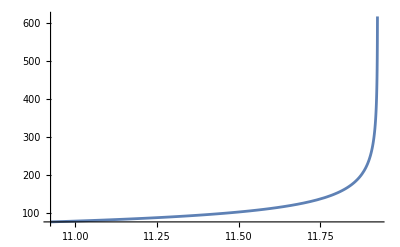

```mathematica
Plot[omega[t],{t,Tinit,Tfin},PlotRange->All]
```

### Solving for the Phase

```mathematica
solphi=NDSolve[{omega[t]-phi'[t]==0,phi[Tinit]==0},phi,{t,Tinit,Tfin}]
```

{{phi→InterpolatingFunction[…]}}

```mathematica
Phiins[t_]:=Evaluate[phi[t]/.solphi]
```

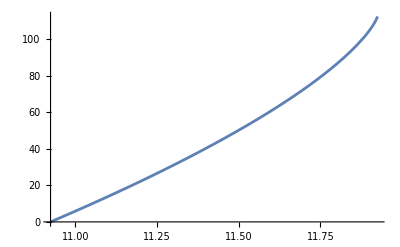

```mathematica
Plot[Phiins[t],{t,Tinit,Tfin},PlotRange->All]
```

### Calculating the binaries separation.

```mathematica
(*This part is non-zero eccentricity ready*)
```

```mathematica
r0pn=1-e*Cos[u]
```

1

```mathematica
r1pn=(2(e*Cos[u]-1))/(e^2-1)+1/6(2(η-9)+e(7η-6)Cos[u])
```

-11/12

```mathematica
r2pn=1/((1-e^2)^2)(1/72(8 η^2+30η+72)e^4+1/72(-16 η^2-876η+756)e^2+1/72(8 η^2+198η+360)+(1/72(-35 η^2+231η-72)e^5+1/72(70 η^2-150η-468)e^3+1/72(-35 η^2+567η-648)e)Cos[u]+(1-e^2)^(1/2)(1/72(360-144η)e^2+1/72(144η-360)+(1/72(180-72η)e^3+1/72(72η-180)e)Cos[u]))
```

43/36

```mathematica
r3pn=1/(181440(1-e^2)^(7/2))((-665280 η^2+1753920η-1814400)e^6+(725760 η^2-77490 π^2 η+5523840η-3628800)e^4+(544320 η^2+154980 π^2 η-14132160η+7257600)e^2-604800 η^2+6854400η+((302400 η^2-1254960η+453600)e^7+(-1542240 η^2-38745 π^2 η+6980400η-453600)e^5+(2177280 η^2+77490 π^2 η-12373200η+4989600)e^3+(-937440 η^2-38745 π^2 η+6647760η-4989600)e)Cos[u]+(1-e^2)^(1/2)((-4480 η^3-25200 η^2+22680η-120960)e^6+(13440 η^3+4404960 η^2+116235 π^2 η-12718296η+5261760)e^4+(-13440 η^3+2242800 η^2+348705 π^2 η-19225080η+16148160)e^2+4480 η^3+45360 η^2-8600904η+((-6860 η^3+550620 η^2-986580η+120960)e^7+(20580 η^3-2458260 η^2+3458700η-2358720)e^5+(-20580 η^3-3539340 η^2-116235 π^2 η+20173860η-16148160)e^3+(6860 η^3-1220940 η^2-464940 π^2 η+17875620η-4717440)e)Cos[u]+116235 π^2 η+1814400)-77490 π^2 η-1814400)
```

(-471521+(38745 π^2)/4)/181440

Radius corrected to 3PN order

```mathematica
r[t_]:=M*(r0pn*xins[t]^-1+r1pn+r2pn*xins[t]+r3pn*xins[t]^2)
```

The final radius in solar masses and in kilograms

```mathematica
{r[Tfin]/M, r[Tfin]*Subscript[M, okm]}
```

{{3.33295},{196.777}}

```mathematica
(*Checking the ISCO separation r=6M*)
```

```mathematica
{6 ,6 M*Subscript[M, okm]}
```

{6,354.24}

```mathematica
(*Time derivative of r used in waveform equations*)
```

```mathematica
rdot [t_]:= r'[t]
```

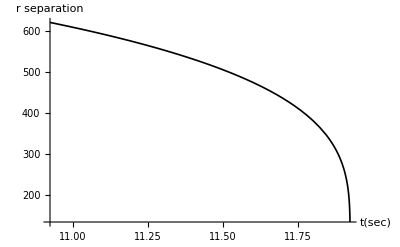

```mathematica
Plot[r [t],{t,Tinit,Tfin},PlotStyle->{Thickness[0.003],Black}, PlotRange->All,AxesLabel->{t[sec],separation r }]
```

### Calculation of the Inspiral Waveform

We will take R = distance to Andromeda=2.401 10^19km, namely 2.5 million light years

```mathematica
R=2.401 10^19
```

2.401×10^19

Strain corrected to 3PN order
ATTENTION: strain needs to be unitless, and we see that we gave sec^-2 because of the derivatives, and omega, so we need to express r in sec. We do this by multiplying wit the mass of the sun in seconds
If we want the express R in km, we need to take M in km as well.

```mathematica
hre[t_]:=-(2.*M*Subscript[M, okm]*η)/R((-(rdot[t]*Subscript[M, os])^2+(r[t]*Subscript[M, os])^2*omega[t]^2+M/r[t])*Cos[2Phiins[t]]+2.*r[t]*rdot[t]*Subscript[M, os]^2*omega[t]*Sin[2Phiins[t]])
```

```mathematica
him[t_]:=-(2.*M*Subscript[M, okm]*η)/R((-(rdot[t]*Subscript[M, os])^2+(r[t]*Subscript[M, os])^2*omega[t]^2+M/r[t])Sin[2Phiins[t]]-2.*r[t]*rdot[t]*Subscript[M, os]^2*omega[t]*Cos[2Phiins[t]])
```

```mathematica
hins[t_]:=hre[t]-ⅈ*him[t]
```

### Expect the Amplitude Evolution to be Smooth

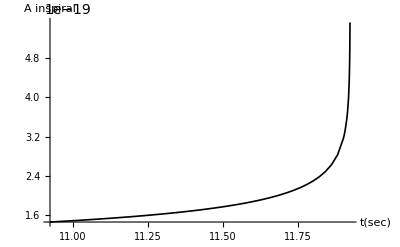

```mathematica
Plot[Abs[hins[t]],{t,Tinit,Tfin},PlotStyle->{Thickness[0.003],Black},PlotRange->All,AxesLabel->{t[sec],inspiral A}]
```

```mathematica
Tinit
```

10.9244

```mathematica
Tfin
```

11.9244

{5.51531×10^-19}

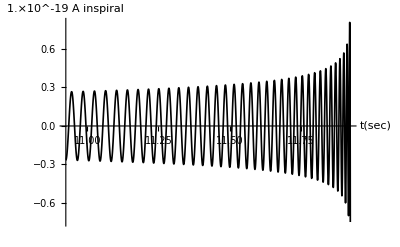

```mathematica
Ahins=Abs[hins[Tfin]]
Plot[hre[t]/Ahins,{t,Tinit,Tfin},PlotStyle->{Thickness[0.003],Black},PlotRange->All,AxesLabel->{t[sec],inspiral A×N[10^-19]}]
```

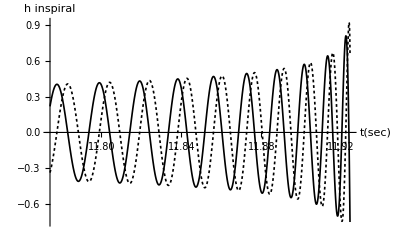

```mathematica
Show[Plot[hre[t]/Ahins,{t,Tfin-0.15,Tfin},PlotStyle->{Thickness[0.003],Black},PlotRange->All],Plot[him[t]/Ahins,{t,Tfin-0.15,Tfin},PlotStyle->{Thickness[0.003],Black,Dashing[Tiny]},PlotRange->All],AxesLabel->{t[sec],inspiral h}]
```

```mathematica
(*Using equation for the dominant mode of the strain*)
```

```mathematica
h22[t_]:= -4(M*Subscript[M, okm]*η)/R Exp[-2*ⅈ*Phiins[t]](π/5)^(1/2)((r[t]*Subscript[M, os]*omega[t]+ⅈ*rdot[t]*Subscript[M, os])^2+M/r[t])
```

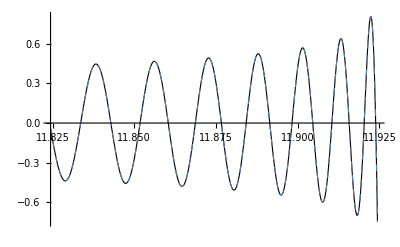

```mathematica
Show[Plot[Re[h22[t]]/Abs[h22[Tfin]],{t,Tfin-0.1,Tfin},PlotStyle->{Thickness[0.002],Black},PlotRange->All],Plot[hre[t]/Ahins,{t,Tfin-0.1,Tfin},PlotStyle->{Thickness[0.002],Dashed},PlotRange->All]](*Dashing[Tiny]*)
```

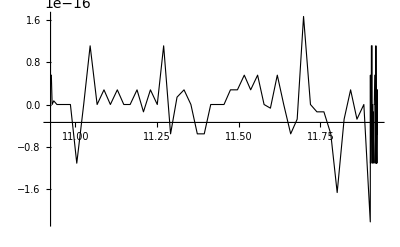

```mathematica
Plot[(Re[h22[t]]/Abs[h22[Tfin]]-hre[t]/Ahins),{t,Tinit,Tfin},PlotStyle->{Thickness[0.002],Black},PlotRange->All]
```

## Calculations for Merger-Ringdown Waveform

Symmetric mass ratio for m1=m2=20
ATTENTION: time is unit less -> measured in units of M, which means that t->t/M
ATTENTION: omega is unit less as well->measured in units of 1/M,  which means that omega-> omega M

```mathematica
N[η]
```

0.25

```mathematica
sfn=N[2*(3)^(1/2)η-390/79 η^2+2379/287 η^3-4621/276 η^4]
```

0.621598

```mathematica
ωqm=N[1-0.63(1-sfn)^0.3]
```

0.529319

```mathematica
(*ωqm=0.3737*)
```

```mathematica
b=N[16014/979-29132/1343 η^2]
```

15.0018

```mathematica
c=N[206/903+180/1141 η^(1/2)+424/1205*η^2/Log[η]]
```

0.291143

```mathematica
k=N[713/1056-23/193 η]
```

0.645397

```mathematica
Q=N[2./(1-sfn)^0.45]
```

3.09707

```mathematica
b2=2*Q/ωqm
```

11.7021

```mathematica
α=N[1/Q^2(16313/562+21345/124 η)]
```

7.51273

```mathematica
α2=72.3/Q^2
```

7.53765

this is when time appears for the first time: time in sec is t->t/(M*M_os)

```mathematica
ts=t/(M*Subscript[M, os])
```

5078.2 t

```mathematica
fs[t_]:=c/2(1+1/k)^(1+k)(1-(1+1/k ⅇ^((-2.*ts)/b))^-k)
```

```mathematica
Simplify[fs[t],Assumptions->{η>0}]
```

0.67895-0.67895/((1+1.54943 ⅇ^(-677.014 t))^0.645397)

```mathematica
N[1-fs[t]]
```

1.-0.67895 (1.-1./((1.+1.54943 2.71828^(-677.014 t))^0.645397))

```mathematica
fs2=Simplify[fs[t]^2,Assumptions->{η>0}]
```

0.460973 (-1+1/((1+1.54943 ⅇ^(-677.014 t))^0.645397))^2

```mathematica
fs4=Simplify[fs2^2]
```

0.212496 (-1+1/((1+1.54943 ⅇ^(-677.014 t))^0.645397))^4

```mathematica
fsdot=D[fs[t],t]
```

-(459.659 ⅇ^(-677.014 t))/((1+1.54943 ⅇ^(-677.014 t))^1.6454)

#### Putting Pieces together for Orbital Frequency Evolution!

```mathematica
ωs[t_]:=ωqm/(M*Subscript[M, os])*(1-fs[t])
```

```mathematica
Simplify[ωs[t]]
```

862.98+1825.01/((1+1.54943 ⅇ^(-677.014 t))^0.645397)

```mathematica
(**Subscript[M, os]*)
```

```mathematica
tmin=-100; tsmin=tmin*M*Subscript[M, os]
tmax=+50; tsmax=tmax*M*Subscript[M, os](*t is in units of the binary mass M*)
```

-0.019692

0.009846

```mathematica
ωs[t]/.t-> tsmin
```

863.232

```mathematica
ωs[t]/.t-> tsmax
```

2685.67

Calculate the frequency in BBH mass

```mathematica
f[t_]:=c/2(1+1/k)^(1+k)(1-(1+1/k ⅇ^((-2.*t)/b))^-k);
f2=Simplify[f[t]^2,Assumptions->{η>0}];
f4=Simplify[f2^2]; fdot=D[f[t],t];
ω[t_]:=ωqm*(1-f[t]);
ω[t]/.t-> tmin
ω[t]/.t-> tmax
```

0.169988

0.528862

```mathematica
N[ωs[t]]
```

2687.99 (1.-0.67895 (1.-1./((1.+1.54943 2.71828^(-677.014 t))^0.645397)))

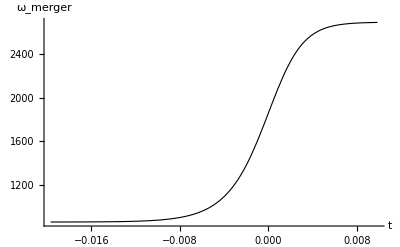

```mathematica
Plot[ωs[t],{t,tsmin,tsmax},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Thickness[0.002],Black},AxesLabel->{t,Subscript[ω, merger]}]
```

#### Integrating to find the Phase

```mathematica
PhiMerge=Integrate[ωs[t],t]
```

862.98 t+7.60195 (1.+1.54943 ⅇ^(-1350802375 t/1995236))^(72271/203808) Hypergeometric2F1[0.354603,1.,1.3546,1.+1.54943 ⅇ^(-677.014 t)]

```mathematica
tsmin
tsmax
```

-0.019692

0.009846

```mathematica
Plot[N[PhiMerge],{t,tsmin,tsmax},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Thickness[0.002],Black},AxesLabel->{t,Subscript[Φ, gIRS]}]
```

-Graphics-

#### Calculation of the Amplitude of the GW

```mathematica
As[t_]:=A0/ωs[t](Abs[fsdot]/(1+α*(fs2-fs4)))^(1/2)
```

```mathematica
A0=1/(M*Subscript[M, os]); (* the amplitude is unitless*)
```

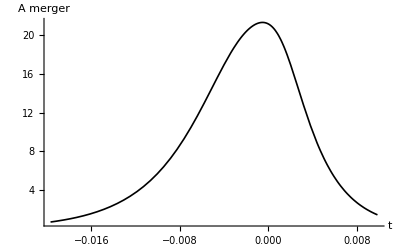

```mathematica
Plot[As[t],{t,tsmin,tsmax},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Thickness[0.003],Black},AxesLabel->{t,merger A}]
```

```mathematica
Amax=MaxValue[As[t],t]
```

21.294

```mathematica
Subscript[t, r]=-ArgMax[As[t],t]
```

0.000538816

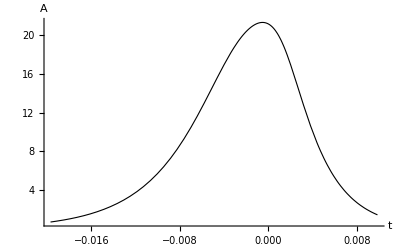

```mathematica
Plot[As[t],{t,tsmin,tsmax},PlotRange->All,AxesOrigin->{Subscript[t, r],0},PlotStyle->{Thickness[0.002],Black},AxesLabel->{t,A}]
```

#### Plugging the pieces into the merger waveform

```mathematica
hmerg[t_]:=As[t]*Exp[-ⅈ*(PhiMerge)]
```

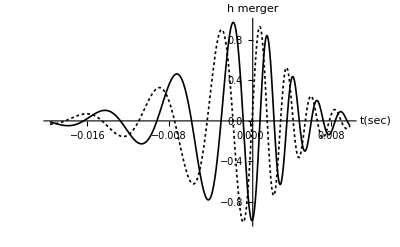

```mathematica
Show[Plot[Re[hmerg[t]]/Amax,{t,tsmin,tsmax},PlotRange->All,AxesOrigin->{Subscript[t, r]/2,0},PlotStyle->{Thickness[0.003],Black},PlotRange->All],Plot[Im[hmerg[t]]/Amax,{t,tsmin,tsmax},PlotRange->All,AxesOrigin->{Subscript[t, r]/2,0},PlotStyle->{Thickness[0.003],Black,Dashing[Tiny]},PlotRange->All],AxesLabel->{t[sec],merger h}]
```

```mathematica
Subscript[f, mmax]=ωs[t]/(2*π)/.t->t0 (*merger frequency at max amplitude*)
```

427.807 (1-0.67895 (1-1/((1+1.54943 ⅇ^(-677.014 t0))^0.645397)))

```mathematica
fISCO=N[1/(π*M*Subscript[M, os])*(1/6)^(3/2)]
```

109.985

```mathematica
Subscript[f, insfin]=Flatten[omega[Tfin]/(π)][[1]](*last frequency for inspiral*)
```

196.046

## Now we do the overlapping

```mathematica
PNfreq=Table[{t-Tfin,omega[t]/(π)},{t,Tfin-0.15,Tfin,0.00005}];
```

```mathematica
PNfreq1=MapAt[Delete[#,0]&,PNfreq,{All,2}];
```

```mathematica
gIRSfreq=Table[{t+τ,ωs[t]/(2*π)},{t,tsmin,tsmax,0.000025}];
```

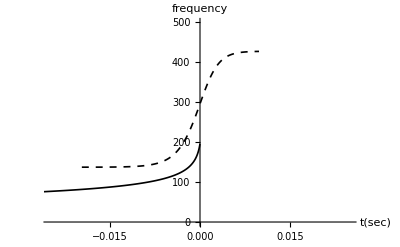

```mathematica
Show[ListLinePlot[PNfreq1,PlotStyle->{Thickness[0.003],Black},PlotRange->{{-0.025,0.025},{0,500}}],ListLinePlot[gIRSfreq/.{τ->0},PlotStyle->{Thickness[0.003],Black, Dashed},PlotRange->{{-0.025,0.025},{0,500}}],
AxesLabel->{t[sec],frequency}]
```

Change the number of steps Ns, and increase  as necessary

```mathematica
Ns=20
```

20

```mathematica
Subscript[f, F]=Flatten[omega[Tfin]/(π)][[1]]
```

196.046

```mathematica
Manipulate[ListPlot[Table[{t+τ,ωs[t]/(2*π)-Subscript[f, F]},{t,-Subscript[t, r]*Ns,Subscript[t, r]*Ns,0.00005}]],{τ,0,Subscript[t, r]*Ns}]
```

Table::iterb: Iterator {t,-Ns t_r,Ns t_r,0.00005} does not have appropriate bounds.

Table::iterb: Iterator {t,-1. Ns t_r,Ns t_r,0.00005} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::nliter: Non-list iterator VectorQ[{t,-Ns t_r,Ns t_r,0.00005}] at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator (#1&)[{t,-1. Ns t_r,Ns t_r,0.00005}] at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

ListPlot::lpn: Table[(#1&)[{t+FE`τ$$183,ωs[t] 0.1591549430918953-1. f_F}],(#1&)[{t,-1. Ns t_r,Ns t_r,0.00005}]] is not a list of numbers or pairs of numbers.

```mathematica
Subscript[f, F]
```

196.046

Here τ is approx 0.003. Change the value for the factor χ until freqM is nearly equal to freqF

```mathematica
0.003/Subscript[t, r]
```

5.56776

```mathematica
χ=5.3512;
Subscript[f, M]=ωs[t]/(2*π)/.t->-t0*χ
```

427.807 (1-0.67895 (1-1/((1+1.54943 ⅇ^(3622.84 t0))^0.645397)))

```mathematica
Subscript[error, f]=(Subscript[f, M]-Subscript[f, F])/Subscript[f, F]*100/.t->-t0*χ(*percent error at frequency matching*)
```

0.510085 (-196.046+427.807 (1-0.67895 (1-1/((1+1.54943 ⅇ^(3622.84 t0))^0.645397))))

Change the value for the variable τ with what you obtained

```mathematica
τ=Subscript[t, r]*χ (*shift for merger time axis*)
```

0.00288331

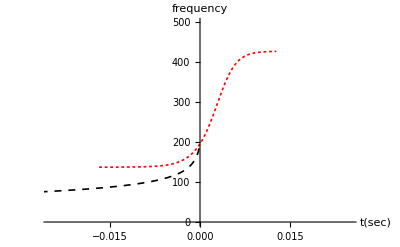

```mathematica
Show[ListLinePlot[PNfreq1,PlotStyle->{Thickness[0.003],Black, Dashed},PlotRange->{{-0.025,0.025},{0,500}}],
ListLinePlot[gIRSfreq,PlotStyle->{Thickness[0.003],Red, Dashing[Tiny]},PlotRange->{{-0.025,0.025},{0,500}}],
AxesLabel->{t[sec],frequency}]
```

```mathematica
(*gIRSfreq{-0.002842+τ,197.02408086748557}*)
```

```mathematica
PNdataRe=Table[{t-Tfin,hre[t]/Ahins},{t,Tfin-0.15,Tfin,0.00005}];
```

```mathematica
PNdataIm=Table[{t-Tfin,him[t]/Ahins},{t,Tfin-0.15,Tfin,0.00005}];
```

```mathematica
PNdataRe1=MapAt[Delete[#,0]&,PNdataRe,{All,2}];
PNdataIm1=MapAt[Delete[#,0]&,PNdataIm,{All,2}];
```

```mathematica
gIRSdataRe=Table[{t+Δ,-Re[hmerg[t]]/Amax},{t,tsmin,tsmax,0.00005}];
gIRSdataIm=Table[{t+Δ,Im[hmerg[t]]/Amax},{t,tsmin,tsmax,0.00005}];
```

Change ξ_+ and ξ_x until you obtain the best match.

```mathematica
SubPlus[ξ]=1.5; Subscript[ξ, x]=1;
```

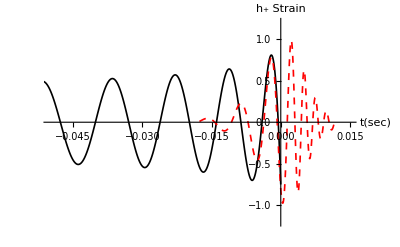

```mathematica
Show[ListLinePlot[PNdataRe1,PlotStyle->{Thickness[0.003],Black},PlotRange->{{-0.05,0.015},{-1.2,1.2}}],ListLinePlot[gIRSdataRe/.{Δ->τ-SubPlus[ξ]*Subscript[t, r]},PlotStyle->{Thickness[0.003],Red, Dashed},PlotRange->All],AxesLabel->{t[sec],Strain SubPlus[h]}]
```

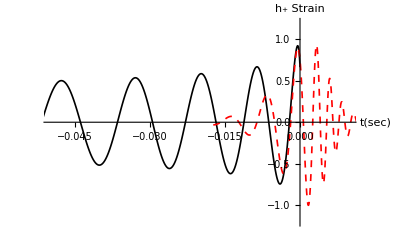

```mathematica
Show[ListLinePlot[PNdataIm1,PlotStyle->{Thickness[0.003],Black},PlotRange->{{-0.05,0.01},{-1.2,1.2}}],ListLinePlot[gIRSdataIm/.{ξ->1,Δ->τ-Subscript[ξ, x]*Subscript[t, r]},PlotStyle->{Thickness[0.003],Red, Dashed},PlotRange->All],AxesLabel->{t[sec],Strain SubPlus[h]}]
```

```mathematica
Tfin+tsmax+τ (*total time*)
```

11.9371